# CO2 Phase Diagram

## PC-SAFT (Perturbed-Chain Statistical Associating Fluid Theory)

Andy Ylitalo, with guidance from Dr. Huikuan Chao and mentorship from Prof. Zhen-Gang Wang

## Questions

## 0. Setup

```mathematica
SetDirectory[FileNameJoin[{"C:","Users","Andy.DESKTOP-CFRG05F","OneDrive - California Institute of Technology", "Documents", "Research", "Wang", "PC-SAFT"}]];
```

## 1. Equations

```mathematica
d[σ_,β_,ϵ_]:=σ(1-0.12Exp[-3ϵ β]);  (* temperature-dependent particle diameter, Gross and Sadowski (2001) *)
```

Note that ξ[ρ,σ,3] represents the total packing fraction and is therefore dimensionless. In general, ξ[ρ,σ,n] has dimensions of (length)^(n-3).

```mathematica
ξ[ρCO2_,ρC5_,dCO2_,dC5_,j_]:=π/6( ρCO2 dCO2^j + ρC5 dC5^j);
```

### Free energy of ideal gas

```mathematica
βfIG[ρ_,N_]:= ρ/N(Log[ρ /N ]-1);
```

Cubed expression is the thermal de Broglie wavelength, λT = h / Sqrt[2 π m k T]. m is the mass of a single particle (in this case, CO2 atom, kg). Note that ρ is divided by N to get the density of molecules, not segments.
7.31*^-26 kg is the mass of a carbon dioxide atom (44.01 amu).

### Free energy of hard-sphere liquid

```mathematica
βfHS[ρCO2_,ρC5_,dCO2_,dC5_]:=6/π( (3 ξ[ρCO2,ρC5,dCO2,dC5,1]ξ[ρCO2,ρC5,dCO2,dC5,2])/(1-ξ[ρCO2,ρC5,dCO2,dC5,3])
+ (ξ[ρCO2,ρC5,dCO2,dC5,2])^3/(ξ[ρCO2,ρC5,dCO2,dC5,3](1-ξ[ρCO2,ρC5,dCO2,dC5,3])^2)
+ ((ξ[ρCO2,ρC5,dCO2,dC5,2])^3/(ξ[ρCO2,ρC5,dCO2,dC5,3])^2-ξ[ρCO2,ρC5,dCO2,dC5,0])Log[1-ξ[ρCO2,ρC5,dCO2,dC5,3]] );
```

### Free energy of association

```mathematica
gCO2[ρCO2_,ρC5_,dCO2_,dC5_]:=1/(1-ξ[ρCO2,ρC5,dCO2,dC5,3])+ 3ξ[ρCO2,ρC5,dCO2,dC5,2] dCO2/ (2(1-ξ[ρCO2,ρC5,dCO2,dC5,3])^2)+ (ξ[ρCO2,ρC5,dCO2,dC5,2])^2dCO2^2 / (2(1-ξ[ρCO2,ρC5,dCO2,dC5,3])^3); 
gC5[ρCO2_,ρC5_,dCO2_,dC5_]:=1/(1-ξ[ρCO2,ρC5,dCO2,dC5,3])+ 3ξ[ρCO2,ρC5,dCO2,dC5,2] dC5/ (2(1-ξ[ρCO2,ρC5,dCO2,dC5,3])^2)+ (ξ[ρCO2,ρC5,dCO2,dC5,2])^2dC5^2 / (2(1-ξ[ρCO2,ρC5,dCO2,dC5,3])^3); (* radial pair distribution function for segments of component i in the hard-sphere system *)
```

```mathematica
βfAssoc[ρCO2_,ρC5_,dCO2_,dC5_,NCO2_,NC5_]:=-(NCO2-1)/NCO2 ρCO2 Log[gCO2[ρCO2,ρC5,dCO2,dC5]]-(NC5-1)/NC5 ρC5 Log[gC5[ρCO2,ρC5,dCO2,dC5]];
```

### Free energy of dispersion

First, load the constants for the polynomial approximation of the integrals I1 and I2 in Gross and Sadowski (2001). We refer to them here as J1 and J2 according to the nomenclature used by Xu et al. (2012).

```mathematica
JConstants=Import[FileNameJoin[{"Data","J_integral_const_a_b.csv"}]];
```

```mathematica
a0=JConstants[[2;;-1, 2]];
a1 = JConstants[[2;;-1, 3]];
a2 = JConstants[[2;;-1, 4]];
b0 = JConstants[[2;;-1, 5]];
b1 = JConstants[[2;;-1, 6]];
b2 = JConstants[[2;;-1, 7]];
```

```mathematica
J1[ρCO2_,ρC5_,dCO2_,dC5_,Nbar_]:=Sum[ (a0[[i]] +(Nbar-1)/Nbar a1[[i]] + (Nbar-1)/Nbar (Nbar-2)/Nbar a2[[i]])(ξ[ρCO2,ρC5,dCO2,dC5,3])^(i-1),{i,1,Length[a0]}]
J2[ρCO2_,ρC5_,dCO2_,dC5_,Nbar_]:=Sum[(b0[[i]] +(Nbar-1)/Nbar b1[[i]] + (Nbar-1)/Nbar (Nbar-2)/Nbar b2[[i]])(ξ[ρCO2,ρC5,dCO2,dC5,3])^(i-1),{i,1,Length[b0]}]
```

```mathematica
M[ρCO2_,ρC5_,dCO2_,dC5_,Nbar_]:=1+Nbar(8 ξ[ρCO2,ρC5,dCO2,dC5,3] - 2 (ξ[ρCO2,ρC5,dCO2,dC5,3])^2)/(1-ξ[ρCO2,ρC5,dCO2,dC5,3])^4+ (1-Nbar)(20 ξ[ρCO2,ρC5,dCO2,dC5,3] - 27(ξ[ρCO2,ρC5,dCO2,dC5,3])^2 + 12 (ξ[ρCO2,ρC5,dCO2,dC5,3])^3 - 2(ξ[ρCO2,ρC5,dCO2,dC5,3])^4)/((1-ξ[ρCO2,ρC5,dCO2,dC5,3])^2(2-ξ[ρCO2,ρC5,dCO2,dC5,3])^2);
```

```mathematica
ϵij[ϵi_,ϵj_,kij_]:=Sqrt[ϵi ϵj](1-kij);
σij[σi_,σj_]:=(σi+σj)/2;
```

```mathematica
βfDisp[ρCO2_,ρC5_,σCO2_,σC5_,ϵCO2_,ϵC5_,kCO2C5_,Nbar_,β_]:=(-π ρCO2^2 (2 J1[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] β ϵCO2 + Nbar /M[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] J2[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] (β ϵCO2)^2) σCO2^3)+(-π ρC5^2 (2 J1[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] β ϵC5 + Nbar /M[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] J2[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] (β ϵC5)^2) σC5^3)+2(-π ρCO2 ρC5 (2 J1[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] β ϵij[ϵCO2,ϵC5,kCO2C5] + Nbar /M[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] J2[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] (β ϵij[ϵCO2,ϵC5,kCO2C5])^2) (σij[σCO2,σC5])^3)
```

### Total Free Energy

```mathematica
Nbar[ρCO2_,ρC5_,NCO2_,NC5_]:=(NCO2 ρCO2 +NC5 ρC5)/(ρCO2+ρC5);
kij[ka_,kb_,β_]:=ka + kb/β; (* careful with the Boltzmann constant here! kb looks like kB. Also, kb is given in Huikuan's slides in terms of β with kB = 1. *)
```

```mathematica
βf[ρCO2_,ρC5_,σCO2_,σC5_,ϵCO2_,ϵC5_,kCO2C5a_,kCO2C5b_,NCO2_,NC5_,β_]:=βfIG[ρCO2,NCO2]+βfIG[ρC5,NC5]+βfHS[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5]]+βfAssoc[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],NCO2,NC5]+βfDisp[ρCO2,ρC5,σCO2,σC5,ϵCO2,ϵC5,kij[kCO2C5a,kCO2C5b,β],Nbar[ρCO2,ρC5,NCO2,NC5],β];
```

### Chemical potential

```mathematica
βμCO2[ρCO2_,ρC5_,σCO2_,σC5_,ϵCO2_,ϵC5_,kCO2C5a_,kCO2C5b_,NCO2_,NC5_,β_]:=D[βf[ρCO2prime,ρC5,σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],ρCO2prime]/.ρCO2prime->ρCO2;
βμC5[ρCO2_,ρC5_,σCO2_,σC5_,ϵCO2_,ϵC5_,kCO2C5a_,kCO2C5b_,NCO2_,NC5_,β_]:=D[βf[ρCO2,ρC5prime,σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],ρC5prime]/.ρC5prime->ρC5;
```

### Pressure

```mathematica
βp[ρCO2_,ρC5_,σCO2_,σC5_,ϵCO2_,ϵC5_,kCO2C5a_,kCO2C5b_,NCO2_,NC5_,β_]:= -βf[ρCO2,ρC5,σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]+ρCO2 βμCO2[ρCO2,ρC5,σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]+ρC5 βμC5[ρCO2,ρC5,σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β];
```

## 2. Parameters

Nondimensionalize length by σCO2, the size of a carbon dioxide bead (2.79 A). Parameters were obtained from 20180426_Huikuan_summary_ternary_syst.ppt

```mathematica
kB=1.38065*^-23;  (* Boltzmann constant [J/K] *)
T=291; (* temperature [K] *)
β=1/T; (* beta parameter *)
NCO2=2; (* number of beads used to model CO2 *)
ϵCO2=170.5 ; (* attractive well depth, from Xu et al. 2012 JCP [K] *)
σCO2= 2.79*^-10; (* bead size [m] *)
σCO2Ref = 1; (* use bead size as reference length for system *)
NC5 = 2; (* number of beads used to model C5H10 *)
σC5=3.92*^-10; (* bead size of cyclopentane [m] *)
σC5Ref = σC5/σCO2; (* nondimensionalized bead size of cyclopentane *)
ϵC5=289.82; (* attractive well depth of cyclopentane, from Xu et al. 2012 JCP [K] *)
kCO2C5a=0.125; (* constant parameter for temperature dependence of interaction [J] *)
kCO2C5b=-2.903*^-6; (* coefficient of temperature for temperature dependence of interaction [J/K] *)
MBeadCO2= 0.044/NCO2; (* molar mass of one bead of carbon dioxide [kg/mol] *)
MBeadC5= 0.071/NC5; (* molar mass of one bead of cyclopentane [kg/mol] *)
NA = 6.022*^23; (* Avogadro's number [molecules/mol] *)
ρCO2Conv=σCO2^3*NA/MBeadCO2; (* convert kg/m^3 -> molecules/σCO2^3 *)
ρC5Conv=σCO2^3*NA/MBeadC5; (* convert kg/m^3 -> molecules/σCO2^3 *)
Pa2MPa = 1*^-6; (* multiplicative conversion from Pa -> MPa *)
pConv = Pa2MPa*kB*T*σCO2^(-3);
```

## 3. Solving for density by setting chemical potentials equal

Test method for solving for coexistence densities and mole fractions.

```mathematica
p=1; (* set the pressure [MPa] *)
ρV0=100;  (* guess for density of vapor phase [kg/m^3] *)
ρL0=1000; (* guess for density of liquid phase [kg/m^3] *)
xCO20=0.1; (* guess for mole fraction of CO2 in liquid phase *)
yCO20=0.94; (* guess for mole fraction of CO2 in vapor phase *)
```

```mathematica
result =FindRoot[{βμCO2[ρL xCO2 ρCO2Conv,ρL(1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμCO2[ρV yCO2 ρCO2Conv,ρV(1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βμC5[ρL xCO2 ρCO2Conv,ρL(1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμC5[ρV yCO2 ρCO2Conv,ρV(1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βp[ρL xCO2 ρCO2Conv,ρL (1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βp[ρV yCO2 ρCO2Conv,ρV (1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βp[ρV yCO2 ρCO2Conv,ρV (1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]pConv==p},{{ρV,ρV0},{ρL,ρL0},{xCO2,xCO20},{yCO2,yCO20}}];
```

```mathematica
result
```

{ρV→19.813+2.70737×10^-27 ⅈ,ρL→777.729-5.36375×10^-25 ⅈ,xCO2→0.0846989-3.38264×10^-27 ⅈ,yCO2→0.935464-2.71368×10^-28 ⅈ}

Now try solving for several coexistence compositions and storing the results in lists.

```mathematica
pList=Range[0.1,6.1,1.5];
ρVList=pList;
ρLList=pList;
xCO2List=pList;
yCO2List=pList;
```

```mathematica
For[i=1,i<=Length[pList],i++,
p=pList[[i]];
result =FindRoot[{βμCO2[ρL xCO2 ρCO2Conv,ρL(1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμCO2[ρV yCO2 ρCO2Conv,ρV(1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βμC5[ρL xCO2 ρCO2Conv,ρL(1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμC5[ρV yCO2 ρCO2Conv,ρV(1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βp[ρL xCO2 ρCO2Conv,ρL (1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βp[ρV yCO2 ρCO2Conv,ρV (1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βp[ρV yCO2 ρCO2Conv,ρV (1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]pConv==p},{{ρV,ρV0},{ρL,ρL0},{xCO2,xCO20},{yCO2,yCO20}}];
ρVList[[i]]=ρV/.result;
ρLList[[i]]=ρL/.result;
xCO2List[[i]]=xCO2/.result;
yCO2List[[i]]=yCO2/.result;
Print[i]]
```

1

2

3

4

5

## Plot

Convert data into desired format: {{x1,y1},{x2,y2},...}

```mathematica
liquidData=Table[{Re[xCO2List[[i]]],pList[[i]]},{i,1,Length[pList]}];
vaporData=Table[{Re[yCO2List[[i]]],pList[[i]]},{i,1,Length[pList]}];
```

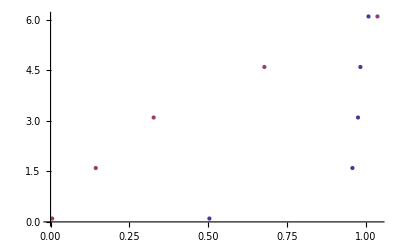

```mathematica
ListPlot[{vaporData,liquidData}]
```

## Export Data

...for better plotting elsewhere.

```mathematica
TList={291,301};
pList=Range[0.1,9,0.5];
T2Save={};
p2Save={};
xCO22Save={};
yCO22Save={};
count=1;
imThresh=0.001; (* threshold of imaginary component above which value is ignored *)
```

```mathematica
For[i=1,i<=Length[TList],i++,
T=TList[[i]];
β=1/T;
pConv = Pa2MPa*kB*T*σCO2^(-3);
For[j=1,j≤Length[pList],j++,
p=pList[[j]];
result =FindRoot[{βμCO2[ρL xCO2 ρCO2Conv,ρL(1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμCO2[ρV yCO2 ρCO2Conv,ρV(1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βμC5[ρL xCO2 ρCO2Conv,ρL(1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμC5[ρV yCO2 ρCO2Conv,ρV(1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βp[ρL xCO2 ρCO2Conv,ρL (1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βp[ρV yCO2 ρCO2Conv,ρV (1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βp[ρV yCO2 ρCO2Conv,ρV (1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]pConv==p},{{ρV,ρV0},{ρL,ρL0},{xCO2,xCO20},{yCO2,yCO20}}];
xCO2=xCO2/.result;
yCO2=yCO2/.result;
If[0≤Re[xCO2]≤1&&0≤Re[yCO2]≤1&&Abs[Im[xCO2]]<imThresh&&Abs[Im[yCO2]]<imThresh, (* only include values that are physical *)
T2Save=Join[T2Save,{T}];
p2Save=Join[p2Save,{p}];
xCO22Save=Join[xCO22Save,{Re[xCO2]}];
yCO22Save=Join[yCO22Save,{Re[yCO2]}];,Null];
Print[count," of ", Length[TList]Length[pList]]
count++;
]]
```

0.00521666-1.41066×10^-15 ⅈ

0.503678-9.28326×10^-16 ⅈ

1 of 10

0.143408

0.957179

2 of 10

$Aborted

```mathematica
T2Save
```

{291,291}

```mathematica
xCO2
```

0.143408

```mathematica
xCO22Save
```

{}

```mathematica
header={"T [K]","p [MPa]","xCO2","yCO2"};
dataTable=Prepend [Table[{T2Save[[i]],p2Save[[i]],xCO22Save[[i]],yCO22Save[[i]]},{i,1,Length[T2Save]}],header];
Export[FileNameJoin[{"Data","co2_c5h10_eos_pred.csv"}],dataTable,"CSV"];
```

```mathematica
xCO2List
```

{{291,0.1,0.00521666,0.503678},{291,1.6,0.143408,0.957179},{291,3.1,0.326897,0.974796},{291,4.6,0.677965,0.982382},{291,6.1,1.0365,1.00809},{301,0.1,0.00326822,0.331852},{301,1.6,0.120448,0.937391},{301,3.1,0.262191,0.962483},{301,4.6,0.46248,0.970845},{301,6.1,0.822219,0.978379}}

{0.00521666-1.41066×10^-15 ⅈ,0.143408,0.326897,0.677965+1.74482×10^-21 ⅈ,1.0365}

For some reason this is not returning real numbers and I cannot restrict the search of FindRoot to real numbers. Instead, I will try FindInstance. Of course, now I cannot supply an initial guess and the solution is VERY SLOW (never waited long enough for this to converge).

```mathematica
result =FindInstance[{βμCO2[ρL xCO2 ρCO2Conv,ρL(1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμCO2[ρV yCO2 ρCO2Conv,ρV(1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]&&βμC5[ρL xCO2 ρCO2Conv,ρL(1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμC5[ρV yCO2 ρCO2Conv,ρV(1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]&&βp[ρL xCO2 ρCO2Conv,ρL (1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βp[ρV yCO2 ρCO2Conv,ρV (1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]&&βp[ρV yCO2 ρCO2Conv,ρV (1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]pConv==p&&0<ρV && ρV < ρL && ρL < 5000 && 0<xCO2 && xCO2<yCO2 && yCO2 <1},{ρV,ρL,xCO2,yCO2}, Reals];
```

$Aborted

Try using NSolve, which allows specification of region but not initial guess. VERY SLOW.

```mathematica
result =NSolve[{βμCO2[ρL xCO2 ρCO2Conv,ρL(1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμCO2[ρV yCO2 ρCO2Conv,ρV(1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βμC5[ρL xCO2 ρCO2Conv,ρL(1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμC5[ρV yCO2 ρCO2Conv,ρV(1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βp[ρL xCO2 ρCO2Conv,ρL (1-xCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βp[ρV yCO2 ρCO2Conv,ρV (1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βp[ρV yCO2 ρCO2Conv,ρV (1-yCO2)ρC5Conv,σCO2Ref,σC5Ref,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]pConv==p,ρL>0,ρL<2500,ρV>0,ρV<ρL,0<xCO2,xCO2<yCO2, yCO2<1},{ρV,ρL,xCO2,yCO2}];
```

$Aborted

```mathematica
result
```

NSolve[{«1»==«16»+(«1»)/π-1/2 Log[(0.131464 (0.000718489 (1-yCO2) ρV+«1»)^2)/(1-1/6 π (0.00100338 (1-yCO2) ρV+«1»))^3+(0.769146 («1»+«1»))/(1-«1»)^2+1/(1-1/6 π (0.00100338 (1-yCO2) ρV+«22» «4» ρV))],«2»,184.997 («1»)==1},«1»]

Can also try solving using FindInstance, which allows the user to specify a domain for the unknown variables

```mathematica
FindInstance[(βμCO2[ρ xCO2,ρ(1-xCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμCO2[ρ yCO2,ρ(1-yCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β])&&(βμC5[ρ xCO2,ρ(1-xCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμC5[ρ yCO2,ρ (1-yCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β])&&(βp[ρ xCO2,ρ (1-xCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βp[ρ yCO2,ρ (1-yCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β])&&(0<ρ<1)&&(0<xCO2)&&(xCO2<yCO2<1),{ρ,xCO2,yCO2}]
```

$Aborted

Set a value for the liquid mole fraction of CO2

```mathematica
xCO2 = 0.1;
```

```mathematica
FindInstance[(βμCO2[ρ xCO2,ρ(1-xCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμCO2[ρ yCO2,ρ(1-yCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β])&&(βμC5[ρ xCO2,ρ(1-xCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμC5[ρ yCO2,ρ (1-yCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β])&&(0<ρ<1)&&(xCO2<yCO2<1),{ρ,yCO2}]
```

$Aborted

Or try solving with FindRoot, which allows the user to guess an initial solution (maybe try to have intelligent guesses based on Huikuan’s model?)

```mathematica
ρ0=0.5;
yCO20=0.2;
```

```mathematica
result=FindRoot[{βμCO2[ρ xCO2,ρ(1-xCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]-βμCO2[ρ yCO2,ρ(1-yCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],βμC5[ρ xCO2,ρ(1-xCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]-βμC5[ρ yCO2,ρ (1-yCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]},{{ρ, ρ0},{yCO2,yCO20}}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
result
```

{ρ→42321.+0.00195845 ⅈ,yCO2→0.0788637+4.56505×10^-15 ⅈ}

Result is complex...

```mathematica
FindInstance[(βμCO2[ρ xCO2,ρ(1-xCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμCO2[ρ yCO2,ρ(1-yCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β])&&(βμC5[ρ xCO2,ρ(1-xCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]==βμC5[ρ yCO2,ρ (1-yCO2),σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]),{ρ,yCO2}]
```

$Aborted

## 4. Plotting

## 2. Numerical Solving

### Critical Point

Occurs where both first and second derivatives of pressure with respect to density are 0.

```mathematica
NSolve[{D[βp[ρ*ρCO2Conv,σCO2Ref,1/(kB Tc),ϵCO2],ρ]==0,D[D[βp[ρ*ρCO2Conv,σCO2Ref,1/(kB Tc),ϵCO2],ρ],ρ]==0},{ρ,Tc}]
```

NSolve[{0.+0.000594471 βp^(1,0,0,0)[0.000594471 ρ,1,(7.24297×10^22)/Tc,2.35401×10^-21]==0,0.000594471 (0.+0.000594471 βp^(2,0,0,0)[0.000594471 ρ,1,(7.24297×10^22)/Tc,2.35401×10^-21])==0},{ρ,Tc}]

## 3. Sanity Checks (thermodynamic relations)